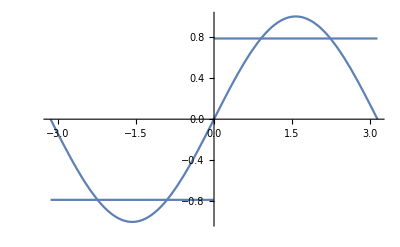
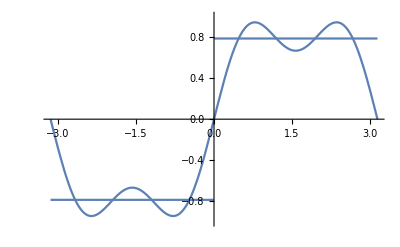
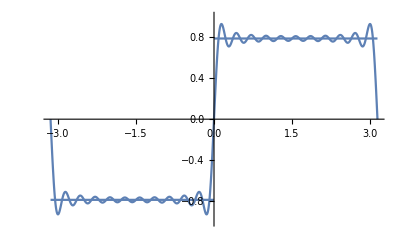
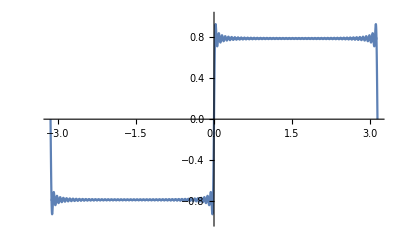

```mathematica
Clear[f,g,x,n];
f[x_]:=Which[-Pi<x≤0,-Pi/4,0<x≤Pi,Pi/4];
g[x_,n_]:=Sum[Sin[(2k+1) x]/(2k+1),{k,0,n}];
Table[Show[Plot[f[x],{x,-Pi,Pi}],Plot[Evaluate[g[x,n]],{x,-Pi,Pi}],PlotRange->{{-Pi,Pi},{-1,1}}],{n,{0,1,10,50}}]
```

(4 k π Cos[2 k π]+(-2+4 k^2 π^2) Sin[2 k π])/(k^3 π^3)

(-2+(2-4 k^2 π^2) Cos[2 k π]+4 k π Sin[2 k π])/(k^3 π^3)

4/3+(4 Cos[π x])/π^2+Cos[2 π x]/π^2+(4 Cos[3 π x])/(9 π^2)+Cos[4 π x]/(4 π^2)+(4 Cos[5 π x])/(25 π^2)-(4 Sin[π x])/π-(2 Sin[2 π x])/π-(4 Sin[3 π x])/(3 π)-Sin[4 π x]/π-(4 Sin[5 π x])/(5 π)

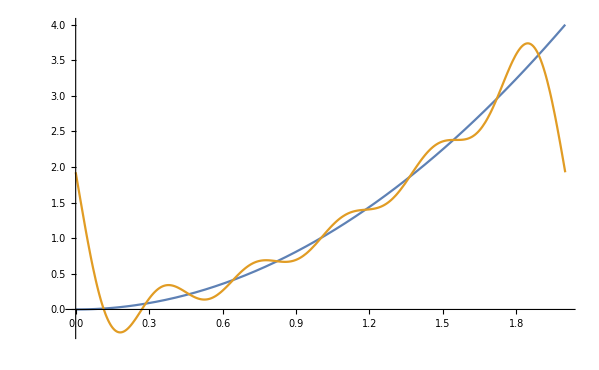

```mathematica
Clear[f,Sn,x,a,b,k,n];
f[x_]:=x^2;
L=1;
a[k_]:=1/L Integrate[f[x] Cos[(k Pi)/L x],{x,0,2}];
b[k_]:=1/L Integrate[f[x] Sin[(k Pi)/L x],{x,0,2}];
Sn[x_,n_]:=a[0]/2+Sum[a[k] Cos[(k Pi)/L x]+b[k] Sin[(k Pi)/L x],{k,1,n}];
a[k]
b[k]
Sn[x,5]
Plot[{f[x],%},{x,0,2}]
```

0

-(8 (2-2 Cos[k π]+k^2 π^2 Cos[k π]-2 k π Sin[k π]))/(k^3 π^3)

(8 (-4+π^2) Sin[(π x)/2])/π^3-(4 Sin[π x])/π+(8 (-4+9 π^2) Sin[(3 π x)/2])/(27 π^3)-(2 Sin[2 π x])/π+(8 (-4+25 π^2) Sin[(5 π x)/2])/(125 π^3)-(4 Sin[3 π x])/(3 π)+(8 (-4+49 π^2) Sin[(7 π x)/2])/(343 π^3)-Sin[4 π x]/π+(8 (-4+81 π^2) Sin[(9 π x)/2])/(729 π^3)-(4 Sin[5 π x])/(5 π)+(8 (-4+121 π^2) Sin[(11 π x)/2])/(1331 π^3)-(2 Sin[6 π x])/(3 π)+(8 (-4+169 π^2) Sin[(13 π x)/2])/(2197 π^3)-(4 Sin[7 π x])/(7 π)+(8 (-4+225 π^2) Sin[(15 π x)/2])/(3375 π^3)-Sin[8 π x]/(2 π)+(8 (-4+289 π^2) Sin[(17 π x)/2])/(4913 π^3)-(4 Sin[9 π x])/(9 π)+(8 (-4+361 π^2) Sin[(19 π x)/2])/(6859 π^3)-(2 Sin[10 π x])/(5 π)+(8 (-4+441 π^2) Sin[(21 π x)/2])/(9261 π^3)-(4 Sin[11 π x])/(11 π)+(8 (-4+529 π^2) Sin[(23 π x)/2])/(12167 π^3)-Sin[12 π x]/(3 π)+(8 (-4+625 π^2) Sin[(25 π x)/2])/(15625 π^3)-(4 Sin[13 π x])/(13 π)+(8 (-4+729 π^2) Sin[(27 π x)/2])/(19683 π^3)-(2 Sin[14 π x])/(7 π)+(8 (-4+841 π^2) Sin[(29 π x)/2])/(24389 π^3)-(4 Sin[15 π x])/(15 π)+(8 (-4+961 π^2) Sin[(31 π x)/2])/(29791 π^3)-Sin[16 π x]/(4 π)+(8 (-4+1089 π^2) Sin[(33 π x)/2])/(35937 π^3)-(4 Sin[17 π x])/(17 π)+(8 (-4+1225 π^2) Sin[(35 π x)/2])/(42875 π^3)-(2 Sin[18 π x])/(9 π)+(8 (-4+1369 π^2) Sin[(37 π x)/2])/(50653 π^3)-(4 Sin[19 π x])/(19 π)+(8 (-4+1521 π^2) Sin[(39 π x)/2])/(59319 π^3)-Sin[20 π x]/(5 π)+(8 (-4+1681 π^2) Sin[(41 π x)/2])/(68921 π^3)-(4 Sin[21 π x])/(21 π)+(8 (-4+1849 π^2) Sin[(43 π x)/2])/(79507 π^3)-(2 Sin[22 π x])/(11 π)+(8 (-4+2025 π^2) Sin[(45 π x)/2])/(91125 π^3)-(4 Sin[23 π x])/(23 π)+(8 (-4+2209 π^2) Sin[(47 π x)/2])/(103823 π^3)-Sin[24 π x]/(6 π)+(8 (-4+2401 π^2) Sin[(49 π x)/2])/(117649 π^3)-(4 Sin[25 π x])/(25 π)

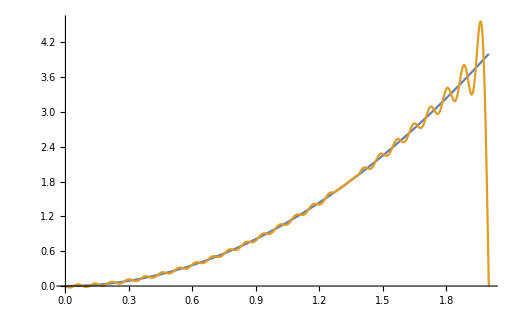

```mathematica
Clear[f,Sn,x,a,b,k,n];
f[x_]:=Which[-2<x<0,-x^2,0≤x≤2,x^2];
L=2;
a[k_]:=1/L Integrate[f[x] Cos[(k Pi)/L x],{x,-2,2}];
b[k_]:=1/L Integrate[f[x] Sin[(k Pi)/L x],{x,-2,2}];
Sn[x_,n_]:=a[0]/2+Sum[a[k] Cos[(k Pi)/L x]+b[k] Sin[(k Pi)/L x],{k,1,n}];
a[k]
b[k]
Sn[x,50]
Plot[{f[x],%},{x,0,2}]
```

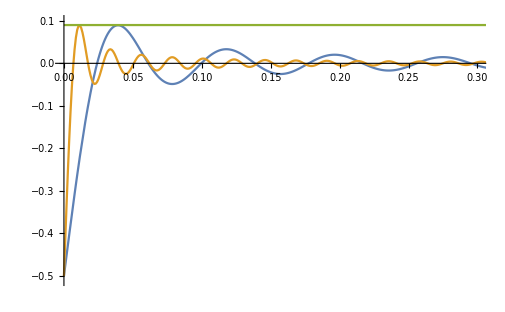

```mathematica
Clear[EN,x];
EN[x_,SN_]:=Sum[(2 Sin[(2 n-1) x])/((2 n-1) Pi),{n,1,SN}]-1/2;
Plot[{EN[x,40],EN[x,140],.09},{x,0,Pi},PlotRange->{{0,0.3},{-0.51,0.1}}]
```

```mathematica
Clear[x,i,data,data1];
data=Table[FindMaximum[{EN[x,k],x>0},{x,0}],{k,1,400,10}];
data1=data;
For[i=1,i<=Length[data],i++,data1[[i]][[2]]=data[[i]][[1]];data1[[i]][[1]]=x/.data[[i]][[2]]]
data1
```

{{1.5708,0.13662},{0.1428,0.0898345},{0.0747998,0.0895844},{0.0506709,0.0895332},{0.0383121,0.0895147},{0.0307999,0.0895059},{0.0257508,0.0895011},{0.0221239,0.0894981},{0.0193925,0.0894962},{0.0172615,0.0894949},{0.0155524,0.089494},{0.0141513,0.0894933},{0.0129818,0.0894927},{0.0119908,0.0894923},{0.0111404,0.089492},{0.0104026,0.0894917},{0.0097565,0.0894915},{0.00918594,0.0894913},{0.00867843,0.0894911},{0.00822407,0.089491},{0.00781491,0.0894909},{0.00744453,0.0894908},{0.00710768,0.0894907},{0.00679999,0.0894907},{0.00651783,0.0894906},{0.00625815,0.0894905},{0.00601838,0.0894905},{0.0057963,0.0894904},{0.00559002,0.0894904},{0.0161938,0.0330947},{0.0156558,0.0330946},{0.00505079,0.0894903},{0.0146803,0.0330945},{0.0142368,0.0330944},{0.0138193,0.0330943},{0.0134256,0.0330943},{0.0130537,0.0330942},{0.0127019,0.0330941},{0.0123685,0.0330941},{0.0361564,0.0112326}}

```mathematica
{FindMaximum[{EN[x,3100],x>0},{x,0}],FindMaximum[{EN[x,12000],x>0},{x,0}],FindMaximum[{EN[x,30000],x>0},{x,0}]}
```

{{0.00532979,{x→0.00962746}},{0.000285514,{x→0.0464694}},{0.0000845603,{x→0.0627795}}}

(8 (2 k π Cos[k π]-2 Sin[k π]+k^2 π^2 Sin[k π]))/(k^3 π^3)

0

4/3-(16 Cos[(π x)/2])/π^2+(4 Cos[π x])/π^2-(16 Cos[(3 π x)/2])/(9 π^2)+Cos[2 π x]/π^2-(16 Cos[(5 π x)/2])/(25 π^2)+(4 Cos[3 π x])/(9 π^2)-(16 Cos[(7 π x)/2])/(49 π^2)+Cos[4 π x]/(4 π^2)-(16 Cos[(9 π x)/2])/(81 π^2)+(4 Cos[5 π x])/(25 π^2)-(16 Cos[(11 π x)/2])/(121 π^2)+Cos[6 π x]/(9 π^2)-(16 Cos[(13 π x)/2])/(169 π^2)+(4 Cos[7 π x])/(49 π^2)-(16 Cos[(15 π x)/2])/(225 π^2)+Cos[8 π x]/(16 π^2)-(16 Cos[(17 π x)/2])/(289 π^2)+(4 Cos[9 π x])/(81 π^2)-(16 Cos[(19 π x)/2])/(361 π^2)+Cos[10 π x]/(25 π^2)-(16 Cos[(21 π x)/2])/(441 π^2)+(4 Cos[11 π x])/(121 π^2)-(16 Cos[(23 π x)/2])/(529 π^2)+Cos[12 π x]/(36 π^2)-(16 Cos[(25 π x)/2])/(625 π^2)+(4 Cos[13 π x])/(169 π^2)-(16 Cos[(27 π x)/2])/(729 π^2)+Cos[14 π x]/(49 π^2)-(16 Cos[(29 π x)/2])/(841 π^2)+(4 Cos[15 π x])/(225 π^2)-(16 Cos[(31 π x)/2])/(961 π^2)+Cos[16 π x]/(64 π^2)-(16 Cos[(33 π x)/2])/(1089 π^2)+(4 Cos[17 π x])/(289 π^2)-(16 Cos[(35 π x)/2])/(1225 π^2)+Cos[18 π x]/(81 π^2)-(16 Cos[(37 π x)/2])/(1369 π^2)+(4 Cos[19 π x])/(361 π^2)-(16 Cos[(39 π x)/2])/(1521 π^2)+Cos[20 π x]/(100 π^2)-(16 Cos[(41 π x)/2])/(1681 π^2)+(4 Cos[21 π x])/(441 π^2)-(16 Cos[(43 π x)/2])/(1849 π^2)+Cos[22 π x]/(121 π^2)-(16 Cos[(45 π x)/2])/(2025 π^2)+(4 Cos[23 π x])/(529 π^2)-(16 Cos[(47 π x)/2])/(2209 π^2)+Cos[24 π x]/(144 π^2)-(16 Cos[(49 π x)/2])/(2401 π^2)+(4 Cos[25 π x])/(625 π^2)

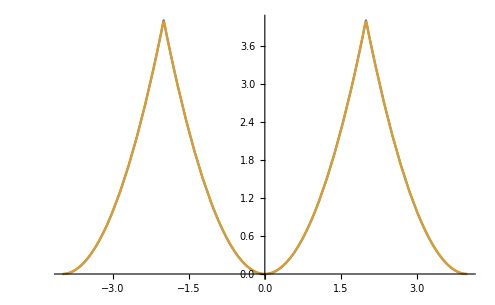

```mathematica
Clear[f,Sn,x,x0,v,L,a,b,k,n,g];
f[x_]:=Which[0≤x≤2,x^2,-2≤x≤0,x^2];
L=2;
F[x_]:=Module[{x0=x},g[t_]:=Which[0≤t≤2,t^2,-2<t<0,t^2];If[Round[x0/4]==0,v=g[x0],v=g[x0-Round[x0/4]*4]];v];
a[k_]:=1/L Integrate[f[x] Cos[(k Pi)/L x],{x,-2,2}];
b[k_]:=1/L Integrate[f[x] Sin[(k Pi)/L x],{x,-2,2}];
Sn[x_,n_]:=a[0]/2+Sum[a[k] Cos[(k Pi)/L x]+b[k] Sin[(k Pi)/L x],{k,1,n}];
a[k]
b[k]
Sn[x,50]
Plot[{F[x],%},{x,-4,4}]
```